```mathematica
(*Completely reseting session or quiting is sometimes necessary to make the code work below. Make sure to run this first in it's own seperate cell*)
Quit[]
```

Remove::rmnsm: There are no symbols matching "Global`*".

Running with 6 parallel kernels

Loading field line data...

Field line data loaded in 0.243687 seconds. Points: 1341

Loading model data...

Model data loaded in 0.335174 seconds

Calculating deltaU (vectorized)...

DeltaU calculated in 0.000222 seconds

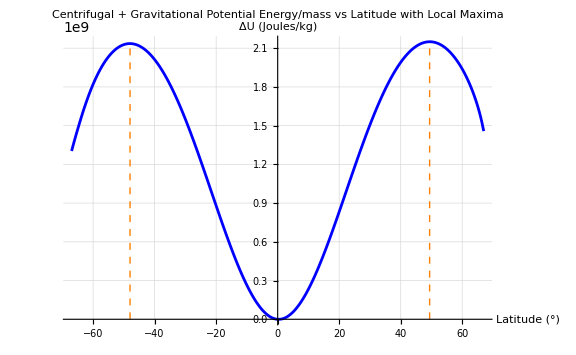

Starting computation...

Processing point 100 of 1341

Processing point 200 of 1341

Processing point 300 of 1341

Processing point 400 of 1341

Processing point 500 of 1341

Processing point 600 of 1341

Processing point 700 of 1341

Processing point 800 of 1341

Processing point 900 of 1341

Processing point 1000 of 1341

Processing point 1100 of 1341

Processing point 1200 of 1341

Processing point 1300 of 1341

Computation completed in 4.5245 seconds

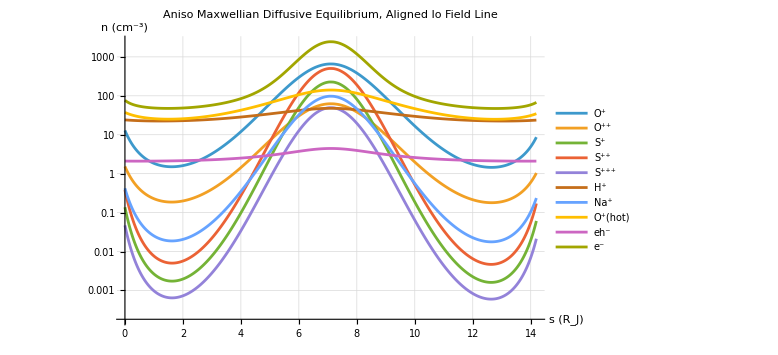

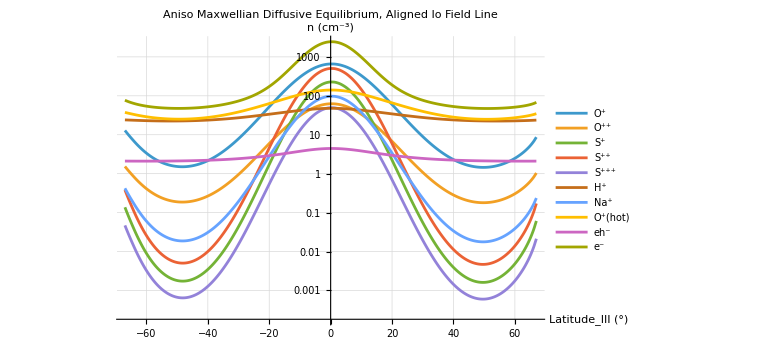

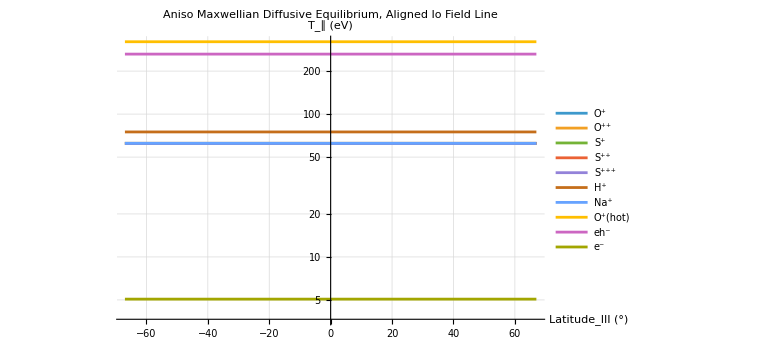

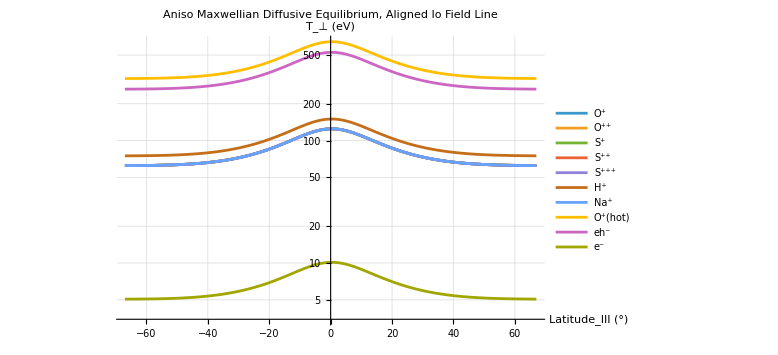

```mathematica
(*Basic Example Use of Diffusive Equilibrium Code*)(* ::Author::*)(*Edward (Eddie) G.Nerney*)(*Nerney (2025)*)(* ::Text::*)(*Diffusive Equilibrium Code for finding steady state plasma Densities at extrapolated location s given plasma parameters at s along same magnetic field line trace.s is arc length along field line.In assumed non inertial rotating frame with planet at Ω in rad/s,or with fraction of corotation fcor given along fixed magnetic field lines given field line traces,including gravitational potential energy (only important close to planet),Centrifugal potential energy,and electrostatic potenial energy.Assumes dynamic accesibility to all locations along field line in steady state,plasma frozen to field line,So No cross-field drift (beyond small gyration around B),No significant scattering to transport particles across field lines,equivalently for MHD Alfvén's theorem frozen-in flux theorem or large magnetic reynolds number,no collisions or sources or losses of particles (no loss cone),no drift or transport (though boundary condition can be informed by),the dist.function same at reference location s0 as s,energy conserved (no sources or losses of energy or dissipation),magnetic moment conserved (adiabatic) or timescales all>>>gyroperiod,Assumes neutrality spatial scales>>>debye length,and assumes plasma frame is the same as the rotating frame.T parallel or Tpar is given T parameter with T perpendicular or Tperp given by A*T.or A=Tperp/Tpar (Anistropy Factor) For Kappa distributions Temps are characterstic temps or T_c not "real" temps.T Where real temps are defined as as Tperp=pperp/n and Tpar=Tpar/n For standard kappas the relation is Tpar=Tpar_c/(1-3/(2*kappa)),Tperp=Tperp_c/(1-3/(2*kappa)) For product kappas there can be different kappa_par and kappa_perp Tpar=Tpar_c/(1-1/(2*kappa_par)),Tperp=Tperp_c/(1-1/(kappa_perp)) kappa parameter given is assumed to be parralel kappa or kappa_par kappa_par=kappa then perp.kappa value is kappa_perp=lambda*kappa lambda=kappa_perp/kappa_par Test Example use of Diffusive Equilibrium MOP community code*)(* ::Section::*)(*Setup and Load Package*)ClearAll["Global`*"]
Remove["Global`*"]
ClearAll["context`*"]

(*Set working directory*)
projDir="/Users/edne8319/Desktop/Diff_Eq_MOP_Community_Code/Mathematica_code";
SetDirectory[projDir];

(*Load ultra-optimized package*)
Get["diffusiveEquilibriumOptimized.wl"];

(*Setup parallel kernels for maximum performance*)
LaunchKernels[];
kernelCount=Length[Kernels[]];
ParallelEvaluate[$HistoryLength=0]; (*Reduce memory usage*)
ParallelEvaluate[$IterationLimit=100000]; (*Increase iteration limit for complex calculations*)
Print["Running with ",kernelCount," parallel kernels"];

(* ::Section::*)
(*Constants and Physical Parameters*)

(*Constants-CODATA RECOMMENDED VALUES OF THE FUNDAMENTAL PHYSICAL CONSTANTS:2022,physics.nist.gov/constants*)
(*Unnecessary precision*)
{kgPerU,ELEMENTARYCHARGE}={1.66053906892*(10^(-27)),1.602176634*(10^(-19))};
{mE,mH,mO,mS,mNa}={5.485799090441*(10^(-4)),1.0078,15.999,32.065,22.990};

(*Even more Unwarranted Unnecessary precision (ignoring electron binding energy decrease too)*)
{mHp,mOp,mO2p,mSp,mS2p,mS3p,mNap}={mH-mE,mO-mE,mO-2*mE,mS-mE,mS-2*mE,mS-3*mE,mNa-mE};

(* ::Section::*)
(*Planet and Field Line Setup*)

(*Planet and species setup*)
planet="Jupiter";
fcor=1.0; (*azimuthal velocity relative to corotation*)
(*perfectly corotating with planet if fcor=1*)
planetParams=DiffusiveEquilibriumOptimized`definePlanet[planet];
RP=planetParams[[1]];
Omega=planetParams[[2]]*fcor;
GM=planetParams[[3]];

(*Load field line data efficiently with packed arrays*)
Print["Loading field line data..."];
loadTiming=AbsoluteTiming[(*Load all datasets in one go and pack them*){s,x,y,z,rho,r,lat,elong,wlong,B}=Developer`ToPackedArray/@(Import["Io_aligned_field_line_trace.h5",{"Datasets",#}]&/@{"/s","/x","/y","/z","/rho","/r","/lat","/elong","/wlong","/B"});
npointsfl=Length[s];];
Print["Field line data loaded in ",loadTiming[[1]]," seconds. Points: ",npointsfl];

(* ::Section::*)
(*Species Setup*)

(*Species setup*)
(*For Singly and doubly ionized Oxygen,Single,doubly,and triply ionized Sulfur protons or H^+,Na^+,the proxy hot O^+(representing both O^{+} S^{++} to match Dougherty (2017) analysis) then a hot electron and core electron population Here hots are treated as their own individual species of distribution type given below (typically Maxwellians) "Proper" Treatment would be to have hots included with cold core as a single kappa,See Nerney (2025)*)
speciesNames={"O+","O++","S+","S++","S+++","H+","Na+","O+(hot)","eh-","e-"};
nspec=Length[speciesNames]; (*Number of species=10*)

(*Mass of each species in u or AMU*)
speciesM={mOp,mO2p,mSp,mS2p,mS3p,mHp,mNap,mOp,mE,mE};

(*Charge of each species in e or elementary charge units*)
speciesQ={1.0,2.0,1.0,2.0,3.0,1.0,1.0,1.0,-1.0,-1.0};

(* ::Section::*)
(*Load Model Data*)

(*Load model data efficiently*)
Print["Loading model data..."];
modelTiming=AbsoluteTiming[(*Create associations for all data*){n0Loaded,T0Loaded,kappa0Loaded,kappatemps0Loaded}=Table[Association[],4];
(*Batch load all species data with packed arrays*)Do[key=speciesNames[[i]];
{n0Loaded[key],T0Loaded[key],kappa0Loaded[key],kappatemps0Loaded[key]}=Developer`ToPackedArray/@(Import["Nerney2025_1D_radial_ceq_reference_model.h5",{"Datasets",#}]&/@{"/n_0/"<>key,"/T_0/"<>key,"/kappa_0/"<>key,"/kappa_temps_0/"<>key});,{i,nspec}];
(*Extract values at reference index*)ioflIdx=191;
{speciesN,speciesT,speciesKappaVals,speciesKappaTemps}=Transpose[Table[{n0Loaded[key][[ioflIdx]],T0Loaded[key][[ioflIdx]],kappa0Loaded[key][[ioflIdx]],kappatemps0Loaded[key][[ioflIdx]]},{key,speciesNames}]];];
Print["Model data loaded in ",modelTiming[[1]]," seconds"];

(* ::Section::*)
(*Distribution Type Selection and Species Creation*)

(*Set all 10 species to distribution type to Anisotropic Maxwellians,They need not all be the same for each species*)
(*speciesType="Maxwellian";*)(*Bagenal& Sullivan (1981) etc.Basic default Assumed isotropic always,ignores anisotropy inputs*)
speciesType="Aniso_Maxwellian";(*Huang& Birmingham (1992) Anisotropic Maxwellian*)
(*speciesType="Aniso_Maxwellian_const_Tperp";*)(*Bagenal& Sullivan (1981),Bagenal (1994),Mei,Thorne,Bagenal (1995) Assumed Constant Anisotropy along field line,inconsistent but good enough often*)
(*speciesType="Aniso_kappa";*)(*Meyer-Vernet et al.(1995);Moncuquet et al.(2002) Anisotropic Standard Kappa distribution*)
(*speciesType="Aniso_product_kappa";*)(*Nerney (2025) Anisotropic Product Kappa Distribution*)
(*speciesType="Fried_Egg"; *)(*Nerney (2025) "Fried-Egg" Distribution Function (Maxwellian limit in parallel of aniso product kappa and still kappa in perp direction)*)

(*Replace Underscores in speciesType string with spaces for nice plot labels*)
niceplotlabel=StringReplace[speciesType,"_"->" "]<>" Diffusive Equilibrium, Aligned Io Field Line";

(*Anisotropy A_0=T_perp0/T_par0=>T_perp0=A_0*T_par0*)
(*Set all to 2 here so Anisotropic*)
speciesA=Table[2.0,nspec];

(*lambda_0=kappa_perp0/kappa_par0 for product kappa only but including for consistency in structures*)
speciesLam=Table[1.,nspec];

(*Create species list with plasma parameters at s_0*)
(*Fill Species class with plasma parameters at s_0 defined above for use with diff_eq code*)
(*Also set to m,q,and T to SI units for calculations.T in Joules as kB=1*)
species0=Table[DiffusiveEquilibriumOptimized`Species[speciesNames[[i]],speciesM[[i]]*kgPerU,(*Convert mass from AMU (u or daltons) to kg*)speciesQ[[i]]*ELEMENTARYCHARGE,(*Convert charge from elementary charges to Coulombs*)speciesT[[i]]*ELEMENTARYCHARGE,(*Convert temperature from eV to Joules*)speciesA[[i]],speciesKappaVals[[i]],speciesLam[[i]],speciesN[[i]],speciesType (*All species set to same distribution type*)],{i,nspec}];

(* ::Section::*)
(*Find Centrifugal Equator and Calculate deltaU*)

(*Find centrifugal equator*)
(*Centrifugal equator defined as where rho=max(rho) or farthest point from spin axis along field line.*)
ceqIdx=First[Flatten[Position[rho,Max[rho]]]];
r0=r[[ceqIdx]];
lat0=lat[[ceqIdx]];
wlong0=wlong[[ceqIdx]];
Pos0={r0,lat0,wlong0};

(*Vectorized calculations*)
Print["Calculating deltaU (vectorized)..."];
deltaUTiming=AbsoluteTiming[deltaU=DiffusiveEquilibriumOptimized`compiledDeltaU[r0,lat0,r,lat,RP,Omega,GM];
(*Magnetic field ratio*)Bratio=B/B[[ceqIdx]];
Pos=Transpose[{r,lat,wlong}];];
Print["DeltaU calculated in ",deltaUTiming[[1]]," seconds"];

(* ::Section::*)
(*Find and Plot Local Maxima*)

(*Find and plot local maxima*)
deltaUFlat=Flatten[deltaU];
latFlat=Flatten[lat];

maxResult=DiffusiveEquilibriumOptimized`findLocalMaxima[deltaUFlat,latFlat];
If[ListQ[maxResult]&&Length[maxResult]==3,{maxIndices,maxLats,maxDeltaU}=maxResult;,{maxIndices,maxLats,maxDeltaU}={{},{},{}};];

fig1=ListLinePlot[Thread[{latFlat,deltaUFlat}],PlotLabel->"Centrifugal + Gravitational Potential Energy/mass vs Latitude with Local Maxima",AxesLabel->{"Latitude (°)","ΔU (Joules/kg)"},GridLines->Automatic,PlotStyle->Blue,ImageSize->Large,Epilog->If[Length[maxLats]>0,{Orange,Dashed,Table[Line[{{maxLats[[i]],Min[deltaUFlat]},{maxLats[[i]],Max[deltaUFlat]}}],{i,Length[maxLats]}]},{}]];
Export["deltaU_vs_latitude.png",fig1,ImageResolution->600];
Print[fig1];

(* ::Section::*)
(*Main Computation Loop-Parallel*)

Print["\nStarting computation..."];

computationTiming=AbsoluteTiming[(*Use parallel computation function*){nOut,phi,TparOut,TperpOut,kappaparOut,kappaperpOut}=DiffusiveEquilibriumOptimized`parallelDiffEq[Pos,Pos0,Bratio,species0,deltaU,planet,fcor,npointsfl];];

Print["Computation completed in ",computationTiming[[1]]," seconds"];

(* ::Section::*)
(*Create Output Associations*)

(*Fixed species labels with proper superscripts and subscripts*)
speciesLabels={Row[{Superscript["O","+"]}," "],Row[{Superscript["O","++"]}," "],Row[{Superscript["S","+"]}," "],Row[{Superscript["S","++"]}," "],Row[{Superscript["S","+++"]}," "],Row[{Superscript["H","+"]}," "],Row[{Superscript["Na","+"]}," "],Row[{Superscript["O","+"],"(hot)"}," "],Row[{Superscript["eh","-"]}," "],Row[{Superscript["e","-"]}," "]};

(*Create associations for plasma parameters*)
n=Association[];
TPar=Association[];
TPerp=Association[];
kappaPar=Association[];
kappaPerp=Association[];

Do[key=speciesNames[[i]];
n[key]=nOut[[i]];
TPar[key]=TparOut[[i]]/ELEMENTARYCHARGE;
TPerp[key]=TperpOut[[i]]/ELEMENTARYCHARGE;
kappaPar[key]=kappaparOut[[i]];
kappaPerp[key]=kappaperpOut[[i]];,{i,nspec}];

(* ::Section::*)
(*Plotting Results*)

(*Plot densities vs s*)
sFlat=Flatten[s];
fig2=ListLogPlot[Table[Thread[{sFlat,Flatten[n[speciesNames[[i]]]]}],{i,nspec}],PlotLegends->speciesLabels,PlotLabel->niceplotlabel,AxesLabel->{Row[{"s (",Subscript["R","J"],")"}],Row[{"n (",Superscript["cm","-3"],")"}]},GridLines->Automatic,ImageSize->Large,PlotRange->All,Joined->True];

Export[speciesType<>"_diff_eq_densities_vs_s_log_aligned_Io_fl.png",fig2,ImageResolution->600];
Print[fig2];

(*Plot densities vs latitude*)
fig3=ListLogPlot[Table[Thread[{latFlat,Flatten[n[speciesNames[[i]]]]}],{i,nspec}],PlotLegends->speciesLabels,PlotLabel->niceplotlabel,AxesLabel->{Row[{Subscript["Latitude","III"]," (°)"}],Row[{"n (",Superscript["cm","-3"],")"}]},GridLines->Automatic,ImageSize->Large,PlotRange->All,Joined->True];

Export[speciesType<>"_diff_all_eq_densities_vs_lat_log_aligned_Io_fl.png",fig3,ImageResolution->600];
Print[fig3];

(*Plot parallel temperatures vs latitude*)
fig4=ListLogPlot[Table[Thread[{latFlat,Flatten[TPar[speciesNames[[i]]]]}],{i,nspec}],PlotLegends->speciesLabels,PlotLabel->niceplotlabel,AxesLabel->{Row[{Subscript["Latitude","III"]," (°)"}],Row[{Subscript["T","∥"]," (eV)"}]},GridLines->Automatic,ImageSize->Large,PlotRange->All,Joined->True];

Export[speciesType<>"_all_diff_eq_Tpar_vs_lat_log_aligned_Io_fl.png",fig4,ImageResolution->600];
Print[fig4];

(*Plot perpendicular temperatures vs latitude*)
fig5=ListLogPlot[Table[Thread[{latFlat,Flatten[TPerp[speciesNames[[i]]]]}],{i,nspec}],PlotLegends->speciesLabels,PlotLabel->niceplotlabel,AxesLabel->{Row[{Subscript["Latitude","III"]," (°)"}],Row[{Subscript["T","⊥"]," (eV)"}]},GridLines->Automatic,ImageSize->Large,PlotRange->All,Joined->True];

Export[speciesType<>"_all_diff_eq_Tperp_vs_lat_log_aligned_Io_fl.png",fig5,ImageResolution->600];
Print[fig5];

(*Plot parallel kappa values vs latitude*)
(*Only plot non-Null values*)
validKappaPar=Select[Table[If[kappaPar[speciesNames[[i]]][[1]]=!=Null,{speciesLabels[[i]],Thread[{latFlat,Flatten[kappaPar[speciesNames[[i]]]]}]},Nothing],{i,nspec}],#=!=Nothing&];

If[Length[validKappaPar]>0,fig6=ListLogPlot[validKappaPar[[All,2]],PlotLegends->validKappaPar[[All,1]],PlotLabel->niceplotlabel,AxesLabel->{Row[{Subscript["Latitude","III"]," (°)"}],Row[{Subscript["κ","∥"]}]},GridLines->Automatic,ImageSize->Large,PlotRange->All,Joined->True];
Export[speciesType<>"_all_diff_eq_kappa_par_vs_lat_log_aligned_Io_fl.png",fig6,ImageResolution->600];
Print[fig6];];

(*Plot perpendicular kappa values vs latitude*)
(*Only plot non-Null values*)
validKappaPerp=Select[Table[If[kappaPerp[speciesNames[[i]]][[1]]=!=Null,{speciesLabels[[i]],Thread[{latFlat,Flatten[kappaPerp[speciesNames[[i]]]]}]},Nothing],{i,nspec}],#=!=Nothing&];

If[Length[validKappaPerp]>0,fig7=ListLogPlot[validKappaPerp[[All,2]],PlotLegends->validKappaPerp[[All,1]],PlotLabel->niceplotlabel,AxesLabel->{Row[{Subscript["Latitude","III"]," (°)"}],Row[{Subscript["κ","⊥"]}]},GridLines->Automatic,ImageSize->Large,PlotRange->All,Joined->True];
Export[speciesType<>"_all_diff_eq_kappa_perp_vs_lat_log_aligned_Io_fl.png",fig7,ImageResolution->600];
Print[fig7];];

(* ::Section::*)
(*Save Results (Optional)*)

(*(*Save dictionary of numpy arrays of plasma paramter outputs*)(*number densities,temperatures,and kappa values*)(*in addition to electrostatic potential phi in volts*)(*and centrifugal+gravitational potential difference per unit mass deltaU*)Export[speciesType<>"Diff_eq_plasma_parameter_along_Io_aligned_fl_JRM33+Con2020.mx",{n,TPar,TPerp,kappaPar,kappaPerp,phi,deltaU}];*)

(*(*Would be read back in like so:*){nLoaded,TParLoaded,TPerpLoaded,kappaParLoaded,kappaPerpLoaded,phiLoaded,deltaULoaded}=Import["Diff_eq_plasma_parameter_along_Io_aligned_fl_JRM33+Con2020.mx"];
(*Then can reference electron density values along field line for example as:nec=n["e-"],etc.see speciesNames above*)*)
```